## This program gets the natural response (V_s=0) of a simple parallel RLC circuit.

### τ = 1/(ω(-ζ±√(ζ^2-1))) Critically Damped Example Values: (L & C must be large for τ to be small enough to graph) L=C, R=0.5; Underdamped Example Values: R = 500kΩ, C = 6uF, L = 9nH; Overdamped Example Values: R = 0.3, C = L = 1;

ζ= 0.122474 < 1 → underdamped

V_c(t) = 1. ⅇ^(-166667. t) (1. Cos[1.35058×10^6 t]+0.123407 Sin[1.35058×10^6 t])

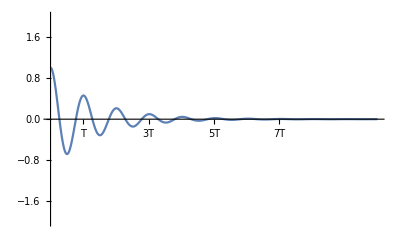

i_c(t) = (3 (1. ⅇ^(-166667. t) (166672. Cos[1.35058×10^6 t]-1.35058×10^6 Sin[1.35058×10^6 t])-166667. ⅇ^(-166667. t) (1. Cos[1.35058×10^6 t]+0.123407 Sin[1.35058×10^6 t])))/500000

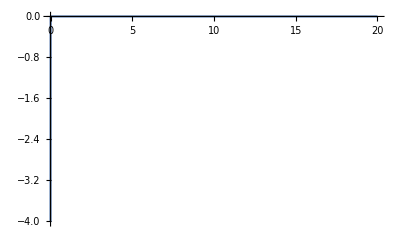

i_L(t) = 100000000/9 ⅇ^(-166667. t) (-1.80003×10^-7 Cos[1.35058×10^6 t]+7.18208×10^-7 Sin[1.35058×10^6 t])

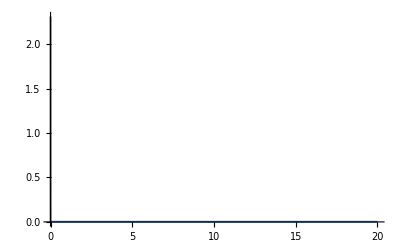

i_R(t) = 2. ⅇ^(-166667. t) (1. Cos[1.35058×10^6 t]+0.123407 Sin[1.35058×10^6 t])

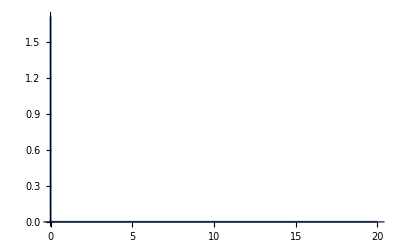

```mathematica
(*This Program gets the natural response of a simple parallel RLC circuit with no external source*)
Clear["Global`*"]
R = 0.5(*Input["Enter The Value Of Resistance"]*);
Capacitor=6*10^-6(*Input["Enter The Value Of Capacitance"]*);
L= 90*10^-9(*Input["Enter The Value Of L"]*);
ωc=1/(√(L Capacitor));
ζ = 1/(2 ωc R Capacitor);
eqn1=V''[t]+2 ζ ωc V'[t]+ωc^2 V[t]==0;
capVoltage = DSolve[{eqn1, V[0]==1, V'[0]==5},V[t],t][[1]];
Vc[t_]:=V[t]/.capVoltage
inductorCurrent=1/L∫Vc[t]ⅆt;
If[ζ<1,output=StringForm["ζ= `` < 1 → underdamped", ζ], If[ζ>1, output=StringForm["ζ= `` > 1 → overdamped", ζ], output=StringForm["ζ=1 →  critically damped", ζ]]];
Style[output,Blue,20, Bold]
Style[StringForm["V_c(t) = ``", Vc[t]], Blue, 18]

Plot[Vc[t],{t,0,10*(2π)/ωc}, PlotRange->{{0, 10*(2π)/ωc}, {-2, 2}}, Ticks->{{{(2π)/ωc,"T"}, {2(2π)/ωc,"2T"}, {3(2π)/ωc,"3T"},{4(2π)/ωc,"4T"},{5(2π)/ωc,"5T"}, {6(2π)/ωc,"6T"},{7(2π)/ωc,"7T"},{8(2π)/ωc,"8T"}}, Automatic}]
CapacitorCurrent=Capacitor D[Vc[t],t];

ic[t_]:=CapacitorCurrent;
Style[StringForm["i_c(t) = ``", ic[t]], Blue, 18]
Plot[ic[t],{t,0,20},  PlotRange->Automatic]

i[t_]:=inductorCurrent;
Style[StringForm["i_L(t) = ``",i[t]], Blue, 18]
Plot[i[t],{t,0,20},  PlotRange->Automatic]

ResistorCurrent=1/R Vc[t];
iR[t_]:=ResistorCurrent;
Style[StringForm["i_R(t) = ``", iR[t]], Blue, 18]
Plot[iR[t],{t,0,20},  PlotRange->Automatic]
```

## This program gets the natural response (V_s=0) of a simple series RLC circuit.

### τ = 1/(ω(-ζ±√(ζ^2-1))) Critically Damped Example Values: (L & C must be large for τ to be small enough to graph) L=C=2, R=2 Underdamped Example Values: R = 0.3, C = L = 2 Overdamped Example Values : R = 5, C = 4, L = 4

ζ= 0.15 < 1 → underdamped

i_L(t) = ⅇ^(-0.15 t) (1. Cos[0.988686 t]-5.91694 Sin[0.988686 t])

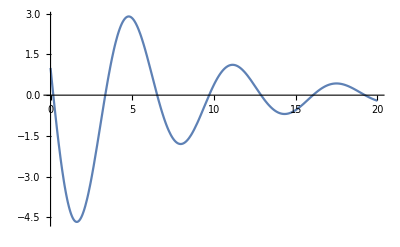

V_L(t) = ⅇ^(-0.15 t) (-6. Cos[0.988686 t]-0.101144 Sin[0.988686 t])

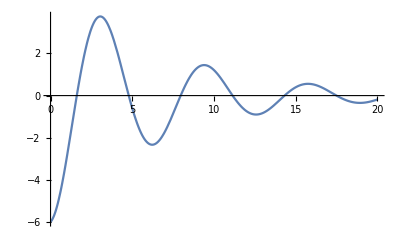

V_R(t) = ⅇ^(-0.15 t) (0.3 Cos[0.988686 t]-1.77508 Sin[0.988686 t])

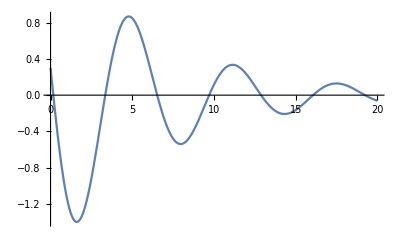

V_c(t) = ⅇ^(-0.15 t) (-6. Cos[0.988686 t]-0.101144 Sin[0.988686 t])

-Graphics-

```mathematica
Clear["Global`*"]

R =Input["Enter The Value Of Resistance"];
Capacitor=Input["Enter The Value Of Capacitance"];
L= Input["Enter The Value Of L"];
ω= 1/(√(L Capacitor));
ζ=R/(2 ω L);
eqn2 =r''[t]+2 ζ ω r'[t]+ω^2 r[t]==0;
inductorCurrent = DSolve[{eqn2,r[0]==1,r'[0]==-6},r[t],t][[1]];
iL[t_]:=r[t]/.inductorCurrent//Simplify;
If[ζ<1,output=StringForm["ζ= `` < 1 → underdamped", ζ], If[ζ>1, output=StringForm["ζ= `` > 1 → overdamped", ζ], output=StringForm["ζ=1 →  critically damped", ζ]]];
Style[output,Blue,20, Bold]
Style[StringForm["i_L(t) = ``", iL[t]], Blue, 18]
Plot[iL[t],{t,0,20},  PlotRange->Automatic]

ResistorVoltage = R*iL[t]//Simplify;
inductorVoltage = L D[iL[t],t]//Simplify;

VL[t_]:=inductorVoltage;
Style[StringForm["V_L(t) = ``", VL[t]], Blue, 18]
Plot[VL[t],{t,0,20},  PlotRange->Automatic]

VR[t_]:=ResistorVoltage;
Style[StringForm["V_R(t) = ``", VR[t]], Blue, 18]
Plot[VR[t],{t,0,20},  PlotRange->Automatic]

CapVoltage = Capacitor D[iL[t],t]//Simplify;

Vc[t_]:=CapVoltage;
Style[StringForm["V_c(t) = ``", Vc[t]], Blue, 18]
Plot[Vc[t],{t,0,20},  PlotRange->Automatic]
```